```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
If[!DirectoryQ["plots"],CreateDirectory["plots"]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
Clear[Δ]
Clear[ω]
dispersion=Solve[0==Det[{{-ω^2+I*η*ω+2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],-ω^2+I*η*ω+2*κ+1/(1-Δ)}}],ω];
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]];
ωmin=3.;
ωmax=4.;
Amin=0.0;
Amax=0.1;
M2=3;
κ=1;
η=0.1;
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;

A1[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(ω^2))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A2[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(ω^2*2*I*n+ω*η))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A3[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*n^2+I*ω*η*n+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-2*κ*(1+(-1)^j*Δ)*Cos[q/2]*(KroneckerDelta[i,j+1]+KroneckerDelta[i,j-1])*KroneckerDelta[n,m]+a*ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A[a_,ω_,Δ_,q_]:=ArrayFlatten[{{A3[a,ω,Δ,q],A2[a,ω,Δ,q]},{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],IdentityMatrix[2*(2*M2+1)]}}]
B[a_,ω_,Δ_,q_]:=ArrayFlatten[{{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],-A1[a,ω,Δ,q]},{IdentityMatrix[2*(2*M2+1)],ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}]}}]

A4[ω_,Δ_,q_,ϵ_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*(ϵ+n)^2+I*ω*η*(ϵ+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-2*κ*(1-(-1)^i*Δ)*Cos[q/2]*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
B4[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];

findroot[a0_,ω_,Δ_,q_]:=Module[{g,a},g[a_?NumericQ]:=Max[Re[Cases[Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;Im[u]≤1&&Im[u]>0]]];
{a,g[a]}/.FindRoot[g[a],{a,a0}]]
```

/Users/zack/Documents/oscillators/snakingoscillators

```mathematica
M=8;
Δ=0.0;
```

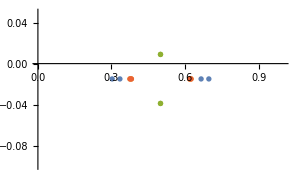
-Graphics- | {{π/2,{0.910484,0.910484,0.910484,0.910484}},{(3 π)/2,{0.910484,0.910484,0.910484,0.910484}},{0,{0.910484,0.910484,0.910484,0.910484}},{π,{0.783569,0.783569,1.05796,1.05796}}}

```mathematica
f[a_,ω_,Δ_,q_]:=Cases[Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;Im[u]≤1&&Im[u]>0]
a=0.06;
ω=3.35;
Grid[{{ListPlot[Table[{Im[#],Re[#]}&/@f[a,ω,Δ,q],{q,0,2*Pi-4*Pi/M,4*Pi/M}],PlotRange->{{0,1},{-0.1,0.05}},ImageSize->300],
SortBy[Table[{q,Abs[Exp[2*Pi*f[a,ω,Δ,q]]]},{q,0,2*Pi-4*Pi/M,4*Pi/M}],Max[#[[2]]]&]}}]
```

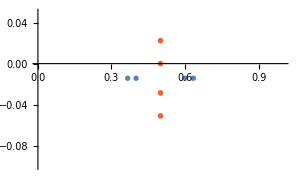
-Graphics- | {{0,{0.914151,0.914151,0.914151,0.914151}},{π/2,{0.726088,0.835672,1.15092,1.}},{(3 π)/2,{0.726088,0.835672,1.15092,1.}},{π,{0.439631,0.439631,1.90085,1.90085}}}

```mathematica
f[a_,ω_,Δ_,q_]:=Cases[Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;Im[u]≤1&&Im[u]>0]
a=0.23737560456708082;
ω=3.5;
Grid[{{ListPlot[Table[{Im[#],Re[#]}&/@f[a,ω,Δ,q],{q,0,2*Pi-4*Pi/M,4*Pi/M}],PlotRange->{{0,1},{-0.1,0.05}},ImageSize->300],
SortBy[Table[{q,Abs[Exp[2*Pi*f[a,ω,Δ,q]]]},{q,0,2*Pi-4*Pi/M,4*Pi/M}],Max[#[[2]]]&]}}]
```

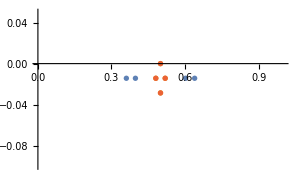
-Graphics- | {{0,{0.914151,0.914151,0.914151,0.914151}},{π/2,{0.914151,0.835672,1.,0.914151}},{(3 π)/2,{0.914151,0.835672,1.,0.914151}},{π,{0.448781,0.448781,1.86209,1.86209}}}

```mathematica
f[a_,ω_,Δ_,q_]:=Cases[Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;Im[u]≤1&&Im[u]>0]
a=0.23038390672785064;
ω=3.5;
Grid[{{ListPlot[Table[{Im[#],Re[#]}&/@f[a,ω,Δ,q],{q,0,2*Pi-4*Pi/M,4*Pi/M}],PlotRange->{{0,1},{-0.1,0.05}},ImageSize->300],
SortBy[Table[{q,Abs[Exp[2*Pi*f[a,ω,Δ,q]]]},{q,0,2*Pi-4*Pi/M,4*Pi/M}],Max[#[[2]]]&]}}]
```

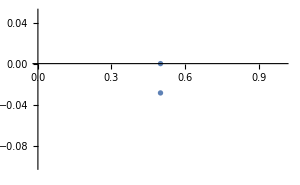
-Graphics- | {{0,{0.497436,1.67996,0.835672,1.}},{π/2,{0.353563,2.36357,0.468287,1.78453}},{(3 π)/2,{0.353563,2.36357,0.468287,1.78453}},{π,{0.318622,0.318622,2.62277,2.62277}}}

```mathematica
f[a_,ω_,Δ_,q_]:=Cases[Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;Im[u]≤1&&Im[u]>0]
a=0.35109740333304307;
ω=3.5;
Grid[{{ListPlot[Table[{Im[#],Re[#]}&/@f[a,ω,Δ,q],{q,0,2*Pi-4*Pi/M,4*Pi/M}],PlotRange->{{0,1},{-0.1,0.05}},ImageSize->300],
SortBy[Table[{q,Abs[Exp[2*Pi*f[a,ω,Δ,q]]]},{q,0,2*Pi-4*Pi/M,4*Pi/M}],Max[#[[2]]]&]}}]
```

{4.15684,Null}

{1.84994,Null}

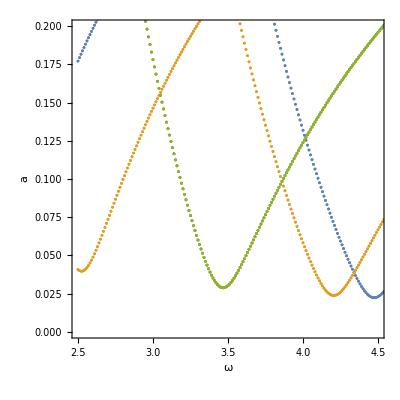

```mathematica
tongues={};
ω0=3.35;
a0=0.15;
ωmin=2.5;
ωmax=5.0;
dω=0.01;

AbsoluteTiming[Monitor[Do[tongue={};
a=a0;
ω=ω0;
continue=True;While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω+dω;If[ω>ωmax||Abs[err]>10^-6,continue=False]; {ω-dω,a,err}];];
a=a0;
ω=ω0;
continue=True;
While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω-dω;If[ω<ωmin||Abs[err]>10^-6,continue=False]; {ω+dω,a,err}];];
AppendTo[tongues,tongue];{ω0,a0}=(First@MinimalBy[tongue,#[[2]]&])[[{1,2}]];,{q,0,Pi-4*Pi/M,4*Pi/M}],{ω,q}]]

AbsoluteTiming[pds=Table[ParallelTable[{evals,evecs}=Eigensystem[{A4[ω,Δ,q,0.5],B4[ω]}];cases=Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]];Transpose[{ConstantArray[ω,Length[cases]],ConstantArray[q,Length[cases]],cases}],{ω,ωmin,ωmax,0.01}] ,{q,0,Pi,4*Pi/M}];]
p0=Show[Table[ListPlot[pds[[i,All,All,{1,3}]],PlotStyle->Directive[PointSize[0.005],ColorData[97,"ColorList"][[i]]]],{i,1,Length[pds]}],PlotRange->{0,0.2}];
Show[p0,ListPlot[SortBy[#,#[[1]]&]&/@tongues[[All,All,{1,2}]],Joined->True],PlotRange->{{2.5,4.5},{0,0.2}},Axes->False,Frame->True,FrameLabel->{"ω","a"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]
```

```mathematica
Cases[Flatten[pds,2],u_/;u[[1]]==3.5]
Cases[Flatten[tongues,1],u_/;u[[1]]==3.5]
```

{{3.5,0,0.351097},{3.5,0,0.351097},{3.5,0,0.31514},{3.5,0,0.31514},{3.5,π/2,0.237376},{3.5,π/2,0.237376},{3.5,π/2,0.230384},{3.5,π/2,0.230384},{3.5,π,0.0302675},{3.5,π,0.0302675},{3.5,π,0.0302675},{3.5,π,0.0302675}}

{}

```mathematica
(* The *)
```

3.5

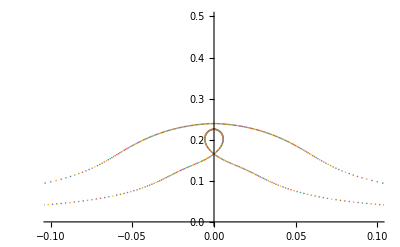

{}

```mathematica
ω=3.5
ϵ=0.5;
q=2*4*Pi/M;
Monitor[test=Table[{evals,evecs}=Eigensystem[{A4[ω,Δ,q,ϵ],B4[ω]}];Transpose[{Im[evals],Re[evals]}],{ϵ,-0.5,0.5,0.001}];,ϵ]
ListPlot[test,PlotRange->{{-0.1,0.1},{0,0.5}}]
cases=Abs[Re[Cases[test,u_/;Abs[Im[u]]<10^-6]]]
```

```mathematica
(*Find the smallest Δ supporting solitons (and the frequency)*)
```

{3.48981,Null}

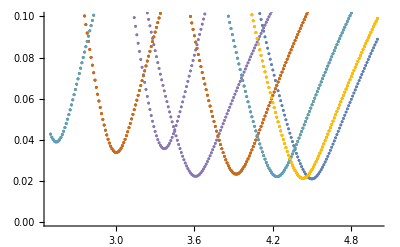

```mathematica
tongues={};
ω0=3.3;
a0=0.1;
ωmin=2.5;
ωmax=5.0;
dω=0.01;
M=16;
Δ=0.2;

AbsoluteTiming[pds=Table[ParallelTable[{evals,evecs}=Eigensystem[{A4[ω,Δ,q,0.5],B4[ω]}];cases=Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]];Transpose[{ConstantArray[ω,Length[cases]],ConstantArray[q,Length[cases]],cases}],{ω,ωmin,ωmax,0.01}] ,{q,0,2*Pi-4*Pi/M,4*Pi/M}];]
p0=Show[Table[ListPlot[pds[[i,All,All,{1,3}]],PlotStyle->Directive[PointSize[0.005],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,1,Length[pds]}],PlotRange->{0,0.1}]
```

```mathematica
SortBy[Cases[Flatten[pds,2],u_/;u[[1]]==3.5],#[[3]]&]
```

{{3.5,π,0.0337678},{3.5,π,0.0337678},{3.5,π,0.0559877},{3.5,π,0.0559877},{3.5,(3 π)/4,0.122276},{3.5,(5 π)/4,0.122276},{3.5,(3 π)/4,0.122276},{3.5,(5 π)/4,0.122276},{3.5,(3 π)/4,0.138565},{3.5,(5 π)/4,0.138565},{3.5,(3 π)/4,0.138565},{3.5,(5 π)/4,0.138565},{3.5,π/2,0.225533},{3.5,(3 π)/2,0.225533},{3.5,π/2,0.225533},{3.5,(3 π)/2,0.225533},{3.5,π/2,0.23926},{3.5,(3 π)/2,0.23926},{3.5,π/2,0.23926},{3.5,(3 π)/2,0.23926},{3.5,π/4,0.28839},{3.5,(7 π)/4,0.28839},{3.5,π/4,0.28839},{3.5,(7 π)/4,0.28839},{3.5,0,0.309811},{3.5,0,0.309811},{3.5,π/4,0.318988},{3.5,(7 π)/4,0.318988},{3.5,π/4,0.318988},{3.5,(7 π)/4,0.318988},{3.5,0,0.348828},{3.5,0,0.348828}}

```mathematica
filebase="data/pendula73";
{M,t1,t0,dt,amp,omega}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
nT=1000;
Grid[{{Grid[{{rasterizeBackground[ListPlot[Transpose[{dt*Range[Length[dat]],Norm[#[[1;;M]]]&/@dat}],Axes->False,Frame->True,FrameLabel->{t,norm},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300]],rasterizeBackground[ListDensityPlot[dat[[-Round[50/dt];;-1;;Round[1/dt],1;;M+1]],InterpolationOrder->0,Frame->True,FrameLabel->{i,t},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300,ColorFunctionScaling->False,ColorFunction->cf]]}}]},{rasterizeBackground[ListPlot[Transpose[{Cos[dat[[1;;nT,1;;M]]]+Transpose[ConstantArray[Range[nT],M]],Sin[dat[[1;;nT,1;;M]]]+2*ConstantArray[Range[M],nT]},{3,2,1}],Joined->True,ImageSize->1000,AspectRatio->1/4,Axes->False]]}}]
```

{32,2000.,1000.,0.05,0.05,3.45}

-Graphics- | -Graphics-
-Graphics-

```mathematica
M=8;
dat=BinaryReadList["auto/pendula/cycle.dat","Real64"];
nT=Length[dat]/(6*M+2)
dat=Transpose[Partition[dat,Length[dat]/(6*M+2)]];
Grid[{{rasterizeBackground[ListDensityPlot[ArcTan[dat[[1;;nT,1;;M]],dat[[1;;nT,M+1;;2*M]]],ColorFunction->cf,ColorFunctionScaling->False,InterpolationOrder->0,AspectRatio->1,ImageSize->350]],rasterizeBackground[ListDensityPlot[ArcTan[dat[[1;;nT,3*M+1;;4*M]],dat[[1;;nT,4*M+1;;5*M]]],ColorFunction->cf,ColorFunctionScaling->False,InterpolationOrder->0,AspectRatio->1,ImageSize->350]]},{rasterizeBackground[ListPlot[Transpose[{dat[[1;;nT,1;;M]]+Transpose[ConstantArray[Range[nT],M]],dat[[1;;nT,2*M+1;;3*M]]+2*ConstantArray[Range[M],nT]},{3,2,1}],Joined->True,ImageSize->350,AspectRatio->1/2,Axes->False]],rasterizeBackground[ListPlot[Transpose[{dat[[1;;nT,3*M+1;;4*M]]+Transpose[ConstantArray[Range[nT],M]],dat[[1;;nT,4*M+1;;5*M]]+2*ConstantArray[Range[M],nT]},{3,2,1}],Joined->True,ImageSize->350,AspectRatio->1/2,Axes->False]]}}]
```

401

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Dimensions[ArcTan[dat[[1;;nT,1;;M]],dat[[1;;nT,M+1;;2*M]]]]
Dimensions[ArcTan[dat[[1;;nT,3*M+1;;4*M]],dat[[1;;nT,4*M+1;;5*M]]]]
```

{401,8}

{401,8}

```mathematica
Dimensions[Riffle[Transpose[ArcTan[dat[[1;;nT,1;;M]],dat[[1;;nT,M+1;;2*M]]]],Transpose[ArcTan[dat[[1;;nT,3*M+1;;4*M]],dat[[1;;nT,4*M+1;;5*M]]]]]]
```

{16,401}

```mathematica
data=Transpose[Riffle[Transpose[ArcTan[dat[[1;;nT,1;;M]],dat[[1;;nT,M+1;;2*M]]]],Transpose[ArcTan[dat[[1;;nT,3*M+1;;4*M]],dat[[1;;nT,4*M+1;;5*M]]]]]];
```

```mathematica
Dimensions[dat]
```

{401,50}

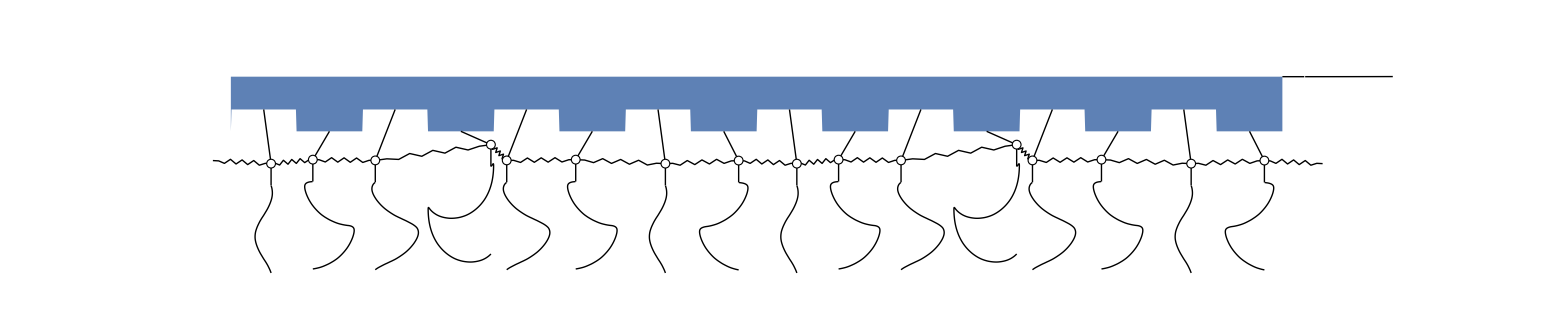

```mathematica
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]]

amax=0.083156978489;
ωd=1;
dx=1.5;
data=Transpose[Riffle[Transpose[ArcTan[dat[[1;;nT,1;;M]],dat[[1;;nT,M+1;;2*M]]]],Transpose[ArcTan[dat[[1;;nT,3*M+1;;4*M]],dat[[1;;nT,4*M+1;;5*M]]]]]];
dn=400;
n0=401;
n=401;
M=16;
dt=1./400;
thetas=data[[n,1;;M]];
thetas2=data[[n-dn;;n,1;;M]];
lengths=Riffle[ConstantArray[0.25,M/2],ConstantArray[-0.25,M/2]];
f[x_]:=lengths[[1+Mod[Round[x/dx]-1,M]]];
z0={0,-amax*Cos[ωd*dt/ωd*(n-n0)]};

p0=Graphics[{ColorData[97,"ColorList"][[1]],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/100}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],Black,Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[dn+1-m,i]]],Cos[thetas2[[dn+1-m,i]]]}-{0,2/dn*m},{m,1,dn}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-amax*Cos[ωd*dt/ωd*(m-n0)],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->2000,PlotRange->{-2+dx*{1/2,M+3.5+1/2},{-3,3}}]
```